# MixedGraph

Make an undirected graph into a mixed graph

## Definition

```mathematica
ClearAll[MixedGraph]
MixedGraph[graph_?GraphQ,threshold_]:=Block[{replaceCount} ,replaceCount=Floor[threshold EdgeCount[graph]];Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,graph,RandomSample[Select[EdgeList[graph],Head[#]==UndirectedEdge&],replaceCount]],EdgeWeight->Thread[EdgeList[graph]->(AnnotationValue[{graph,#1},EdgeWeight])&/@EdgeList[graph]]]]/;0<=threshold<=1
```

## Documentation

### Usage

MixedGraph[graph, threshold]

randomly replaces a part of a graph's undirected edges with directed graphs up to threshold.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Generate a random spatial graph and take the largest connected component by edge count:

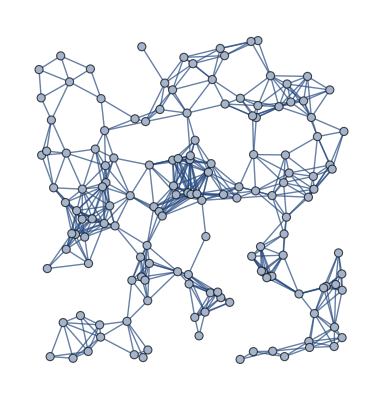

```mathematica
First[TakeLargestBy[ConnectedGraphComponents@RandomGraph[SpatialGraphDistribution[148,ⅇ^-2]],EdgeCount,1]]
```

Make the graph mixed with a threshold of 50%:

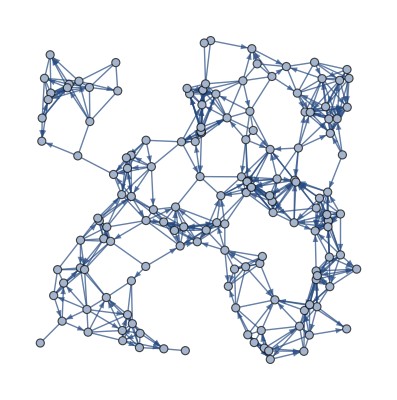

```mathematica
Graph[MixedGraph[First[TakeLargestBy[ConnectedGraphComponents@RandomGraph[SpatialGraphDistribution[148,ⅇ^-2]],EdgeCount,1]],.5],ImageSize->Full]
```

Make a parametric Harary graph mixed:

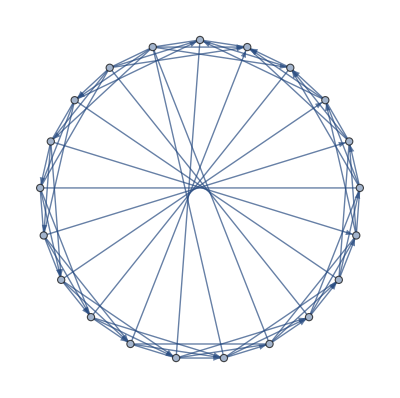

```mathematica
MixedGraph[HararyGraph[7,21],.5]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

### Options

### Applications

Find a Chinese postman tour on a random mixed graph.

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

keyword 1

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics
 Wolfram Physics Project |

### Related Symbols

RandomGraph

SpatialGraphDistribution

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

I am creating this function to start working on a generalized version of FindPostmanTour for mixed weighted graphs for the NP-hard Mixed Chinese Postman Problem MCPP.